```mathematica
"2.3.2. Newton-Raphson method.
Test (fiction α), for example α = 4"
```

```mathematica
f[x_]:=-4-4*4+(9+4)x+6 x^2+x^3
```

```mathematica
x={{4},{3}}; (*начальные приближения*)
n=0.0001; (*точность*)
```

```mathematica
For[i=2,First@Abs[x[[i]]-x[[i-1]]]>n,i++,
x=Append[x,{}];
x[[i+1]]=x[[i]]-f[x[[i]]]/f'[x[[i]]]
];
```

```mathematica
res=Flatten@Map[N,x] (*перевод вектора корней к нормальному виду*)
```

{4.,3.,1.68421,1.11634,1.00415,1.00001,1.}

```mathematica
NSolve[f[k]==0,k,Reals] (*проверка через встоенный оператор*)
```

{{k→1.}}

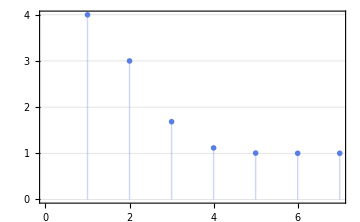

```mathematica
Show[ListPlot[Table[res[[i]],{i,1,Length@res}],PlotTheme->"Business",Filling->Axis],ImageSize->Medium]
```